# Volume Measurement

When does counting vertices give geometric volume? We compare the count of a graph ball with the count of its interior, first on a lattice and then on graphs sampled from a continuum. The scale comparison keeps physical radius fixed while the graph spacing decreases.

## Two measures of one ball

For a vertex set X, its graph boundary ∂X consists of vertices in X with a neighbour outside X. Its interior is IntX==X\∂X. InfraMeasurement gives the counting measure Abs[X] and the Riemannian measure Abs[IntX]. They differ by the boundary count.

```mathematica
Needs[ "WolframInstitute`InfraGeometry`" ]
```

Here the ball is B_r(c)=={v:d(c,v)≤r}, where d is graph distance. The gallery compares two tilings, a planar mesh, a sphere mesh, a spatial mesh and a Sierpinski graph. Each ball has half the graph radius, rounded down. The graph constructions use their default layouts; no coordinates enter the measurement. The interior is green and the boundary blue. Counting includes both colours; the Riemannian measure includes only green.

```mathematica
GraphicsGrid[ Partition[ Table[
  With[
    { graph = BlockRandom[ InfraSubstrate[ name, "Large" ], RandomSeeding -> 2 ] },
    { centre = First @ GraphCenter[ graph ], radius = Floor[ GraphRadius[ graph ] / 2 ] },
    { vertices = Keys @ InfraMeasurement[ graph, InfraBall[ centre, radius ], "VertexDensity" ] },
    Labeled[ InfraSubstrateHighlight[ graph,
      { InfraInterior[ graph, vertices ] -> StandardGreen, InfraBoundary[ graph, vertices ] -> StandardBlue } ,
      "ThicknessRange" -> { 1.25, 5 } ], name ] ],
  { name, { "SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph",
    "SphereMeshGraph", "CubeMeshGraph", "SierpinskiTriangleGraph" } } ], 3 ], ImageSize -> 1200 ]
```

-Graphics-

For every undirected graph and integer r≥1,

B_(r-1)(c)⊆Int B_r(c)⊆B_r(c).

A vertex at distance at most r-1 has every neighbour at distance at most r. An outer-layer vertex also belongs to the interior when it has no neighbour at distance r+1. Thus the interior equals B_(r-1) only when every outer-layer vertex has an outward neighbour. This holds for an untruncated square-lattice ball, but it need not hold on a mesh.

## Tubes and ellipsoids

A volume measurement also depends on the region being measured. Let I(c,p) be the union of shortest paths from c to p, and let n==d(c,p). The tube T_s(I)=={x:d(x,I)≤s} is contained in the ellipsoid

E_(2s)=={x:d(c,x)+d(x,p)≤n+2s}.

Indeed, if y∈I and d(x,y)≤s, the triangle inequalities through y give d(c,x)+d(x,p)≤n+2s. The pictures show the tube in green, the excess of the ellipsoid in red, and the interval in blue. The same six substrates compare the two regions, using only graph distance. The endpoint separation and tube thickness are chosen in proportion to the graph radius. Each caption reports whether the inclusion is strict for the displayed regions.

```mathematica
GraphicsGrid[ Partition[ Table[
  With[
    { graph = BlockRandom[ InfraSubstrate[ name, "Large" ], RandomSeeding -> 2 ] },
    { centre = First @ GraphCenter[ graph ], length = Floor[ GraphRadius[ graph ] / 3 ] },
    { endpoint = RandomInfraPoint[ graph, InfraShell[ centre, length ], RandomSeeding -> 1 ],
      thickness = Ceiling[ length / 2 ] },
    { ellipsoid = Keys @ InfraMeasurement[ graph,
        InfraQuadric[ { centre, endpoint }, length + 2 thickness ], "VertexDensity" ],
      tube = Keys @ InfraMeasurement[ graph, InfraTube[ InfraSegment[ centre, endpoint ], thickness ], "VertexDensity" ] },
    Labeled[ InfraSubstrateHighlight[ graph,
      { Complement[ ellipsoid, tube ] -> StandardRed, tube -> StandardGreen,
        InfraSegment[ centre, endpoint ] -> StandardBlue } ,
      "ThicknessRange" -> { 1.25, 5 } ],
      Column[ { name, If[ Complement[ ellipsoid, tube ] === { }, "tube = ellipsoid", "tube strictly inside ellipsoid" ] },
        Alignment -> Center ] ] ],
  { name, { "SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph",
    "SphereMeshGraph", "CubeMeshGraph", "SierpinskiTriangleGraph" } } ], 3 ], ImageSize -> 1200 ]
```

-Graphics-

On the square lattice, the interval is a coordinate rectangle and

d(c,x)+d(x,p)-d(c,p)==2d(x,I(c,p)).

This follows by clamping each coordinate of x to the interval between the corresponding coordinates of the endpoints. Thus the ellipsoid and tube coincide there. Where red vertices appear, the inclusion is strict. The meshes, sphere and fractal show the dependence on the substrate.

## An exact rescaling limit

On the square lattice, the shell at distance k≥1 has 4k vertices. Hence the closed ball has

L(r)==1+∑_(k==1)^r 4k==2 r^2+2r+1

vertices, and its interior has L(r-1)==2 r^2-2r+1 for r≥1. Give each edge physical length a and each vertex area a^2. At the physical radius R==ar the two masses are

a^2 L(r)  |  ==2 R^2+2aR+a^2, 
 a^2 L(r-1)  |  ==2 R^2-2aR+a^2.

Both converge to 2 R^2 as a→0 with R fixed. This is the area of the taxicab ball |x|+|y|≤R. Refining a by a factor b and multiplying r by b preserves this area; the linear error shrinks by b and the quadratic error by b^2. The limiting geometry retains its diamond-shaped balls.

The top row keeps R==1/4 fixed while refining the lattice; the red diamond is unchanged. Each finite grid includes an extra layer beyond the measured ball. Below each graph, the two area profiles are compared with the red continuum curve 2 R^2. The blue and green curves close around it as the lattice refines. The dashed gray curve assigns full weight to interior vertices and half weight to boundary vertices. It is the mean of the two measured profiles.

```mathematica
GraphicsGrid[ Transpose[ Table[
  With[
    { spacing = 1 / ( 4 radius ) },
    { graph = GridGraph[ { 2 radius + 3, 2 radius + 3 }, Sequence @@ InfraSubstrateStyle[ "Large" ],
        VertexCoordinates -> spacing Tuples[ Range[ -radius - 1, radius + 1 ], 2 ] ] },
    { centre = First @ GraphCenter[ graph ] },
    { ball = InfraBall[ centre, radius ], regions = Table[ InfraBall[ centre, r ], { r, 1, radius } ] },
    { vertices = Keys @ InfraMeasurement[ graph, ball, "VertexDensity" ],
      profiles = Map[ measure |-> spacing^2 InfraMeasurement[ graph, regions, measure ],
        { "CountingMeasure", "RiemannianMeasure" } ] },
    { Labeled[ InfraSubstrateHighlight[ graph,
        { InfraInterior[ graph, vertices ] -> StandardGreen, InfraBoundary[ graph, vertices ] -> StandardBlue },
        Epilog -> { StandardRed, AbsoluteThickness[ 1.5 ],
          Line[ { { 1/4, 0 }, { 0, 1/4 }, { -1/4, 0 }, { 0, -1/4 }, { 1/4, 0 } } ] },
        PlotRange -> { { -3/8, 3/8 }, { -3/8, 3/8 } } ,
      "ThicknessRange" -> { 1.25, 5 } ], Row[ { "r = ", radius } ] ],
      Show[
        ListLinePlot[ Map[ values |-> Transpose[ { spacing Range[ radius ], values } ], Append[ profiles, Mean[ profiles ] ] ],
          PlotStyle -> { StandardBlue, StandardGreen, Directive[ StandardGray, Dashed ] }, PlotMarkers -> Automatic,
          PlotLegends -> { "counting", "interior", "half boundary" }, AxesLabel -> { "R", "area" },
          PlotRange -> { { 0, 1/4 }, { 0, 1/5 } } ],
        Plot[ 2 physicalRadius^2, { physicalRadius, 0, 1/4 }, PlotStyle -> StandardRed ] ] } ],
  { radius, { 4, 8, 16 } } ] ], ImageSize -> 1000 ]
```

-Graphics-

The gap between the two masses is 4aR, the area assigned to one graph layer. Their mean satisfies

a^2(Abs[Int B_r|+1/2|∂B_r])==2 R^2+a^2.

Thus half weight on the boundary removes the first-order error for these square-lattice balls. At fixed R, halving the spacing divides the remaining error by four. No such cancellation has been established here for an arbitrary mesh.

## A sampled disk at three resolutions

Sample the unit square uniformly and join points within ϵ==N^(-1/3). Use r==Round((1/4)/ϵ) and compare the graph ball with the disk of radius R_N==ϵr about the chosen centre. The prescribed edge scale supplies the length unit. There is no fitted hop length. The convergence argument below applies inside this convex domain when the reference disk stays inside the square.

```mathematica
ripsVolumes = Table[
  With[
    { points = BlockRandom[ RandomPoint[ Rectangle[], count ], RandomSeeding -> 2 ],
      epsilon = count^(-1/3) },
    { graph = NearestNeighborGraph[ points, { All, epsilon } ], nearest = Nearest[ points ],
      centre = First @ Nearest[ points, { 1/2, 1/2 } ], radius = Round[ ( 1/4 ) / epsilon ] },
    { ball = InfraBall[ centre, radius ] },
    { vertices = Keys @ InfraMeasurement[ graph, ball, "VertexDensity" ] },
    { interior = InfraInterior[ graph, vertices ] },
    <| "N" -> count, "Radius" -> epsilon radius,
      "Counting" -> N[ InfraMeasurement[ graph, ball, "CountingMeasure" ] / count ],
      "Riemannian" -> N[ InfraMeasurement[ graph, ball, "RiemannianMeasure" ] / count ],
      "Disk" -> N[ Pi ( epsilon radius )^2 ],
      "Picture" -> Graphics[ {
        Map[ cell |-> With[ { owner = First @ nearest[ RegionCentroid[ cell ] ] },
          { EdgeForm[ Directive[ StandardGray, Opacity[ 0.3 ] ] ],
            Which[ MemberQ[ interior, owner ], Lighter[ StandardGreen, 0.5 ],
              MemberQ[ vertices, owner ], Lighter[ StandardBlue, 0.5 ], True, FaceForm[] ], cell } ],
          MeshPrimitives[ VoronoiMesh[ points, { { 0, 1 }, { 0, 1 } } ], 2 ] ],
        StandardGray, PointSize[ 0.002 ], Point[ points ],
        StandardRed, AbsoluteThickness[ 1.5 ], Circle[ centre, epsilon radius ] },
        PlotRange -> { { 0, 1 }, { 0, 1 } }, AspectRatio -> 1 ] |> ],
  { count, { 400, 1600, 6400 } } ];
GraphicsRow[ Map[ data |-> Labeled[ data[ "Picture" ], Row[ { "N = ", data[ "N" ] } ] ], ripsVolumes ],
  ImageSize -> 1000 ]
```

-Graphics-

Each vertex is drawn with its nearest-point cell. Green cells belong to interior vertices and blue cells to boundary vertices; the red circle is the reference disk. The cells show the sampling scale; each vertex still receives mass 1/N, not the area of its drawn cell. The plot compares the two counts with the disk area, so agreement would put both curves on the horizontal line at one.

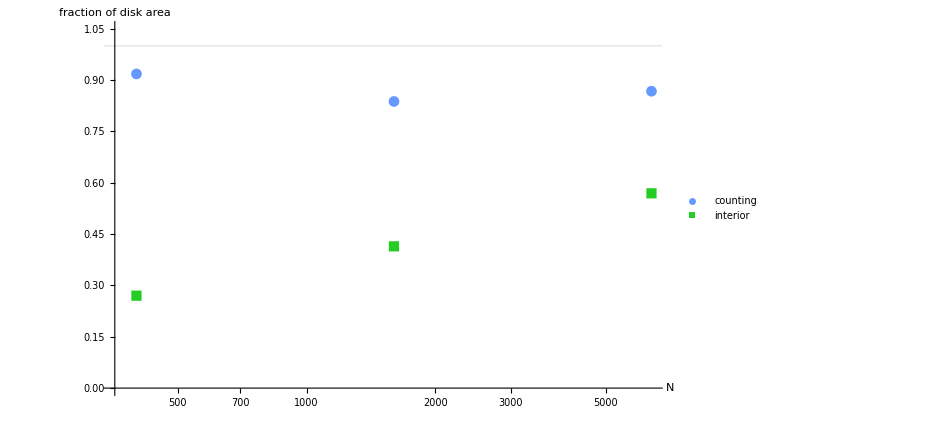

```mathematica
ListLogLinearPlot[
  Map[ measure |-> Map[ data |-> { data[ "N" ], data[ measure ] / data[ "Disk" ] }, ripsVolumes ],
    { "Counting", "Riemannian" } ],
  PlotStyle -> { StandardBlue, StandardGreen }, PlotMarkers -> Automatic,
  PlotLegends -> { "counting", "interior" }, AxesLabel -> { "N", "fraction of disk area" },
  GridLines -> { None, { 1 } }, PlotRange -> { 0, 1.05 }, ImageSize -> 700 ]
```

The gap between the curves narrows, and both remain below the reference disk area. The finite samples illustrate agreement of the two conventions but do not establish the volume limit.

## Why both measures can converge

Let M be a compact connected Riemannian manifold without boundary, with distance d and normalized volume μ. Let V_N⊂M be a sample of N vertices, with mesh

h_N==sup_(x∈M) min_(v∈V_N) d(x,v).

Join two vertices when their distance is less than ϵ_N, and write H_N for graph distance. Assume ϵ_N→0 and h_N/ϵ_N→0. For 2 h_N<ϵ_N,

d(u,v)≤ϵ_N H_N(u,v)≤ϵ_N/(ϵ_N-2 h_N)d(u,v)+ϵ_N.

The first inequality adds the lengths of the graph edges. For the second, divide a minimizing geodesic into m==⌊d(u,v)/(ϵ_N-2 h_N)⌋+1 equal pieces. Each piece is shorter than ϵ_N-2 h_N. Replace each internal subdivision point by a sample point within h_N, keeping the two endpoints. Delete consecutive repetitions among the chosen sample points. Successive remaining points are adjacent. The resulting number of edges is at most d(u,v)/(ϵ_N-2 h_N)+1. The scaled graph distance therefore converges uniformly to d on sampled pairs.

Distance convergence alone does not identify volume. Also assume that ν_N==N^-1∑_(v∈V_N) δ_v converges weakly to μ. A dense sample concentrated in one region can violate this assumption.

Choose centres c_N∈V_N with c_N→c and integers r_N with ϵ_N r_N→R>0. Assume μ(∂B_R(c))==0. The distance bound places both graph balls B_r_N(c_N) and B_(r_N-1)(c_N) between sampled metric balls whose radii tend to R. Weak convergence and the zero boundary volume give

Abs[B_r_N(c_N)]/N⟶μ(B_R(c)),    Abs[B_(r_N-1)(c_N)]/N⟶μ(B_R(c)).

The interior lies between these two graph balls, so its normalized count has the same limit. This proves agreement under the stated distance and sampling assumptions. It does not require the interior to equal the ball one radius earlier.

## Consequence for dimension

For positive radii, define

Δ(r)==(logV(r+1)-logV(r))/(log(r+1)-logr).

On the square lattice, substituting the two polynomials gives Δ(r)==2-1/r+O(r^-2) for counting and Δ(r)==2+1/r+O(r^-2) for the interior. Both read dimension two when many graph layers are resolved. Their difference at small radii comes from the boundary convention.

LogDifferenceQuotients assigns radii one, two, and so on to its input list. The profiles below therefore start at radius one.

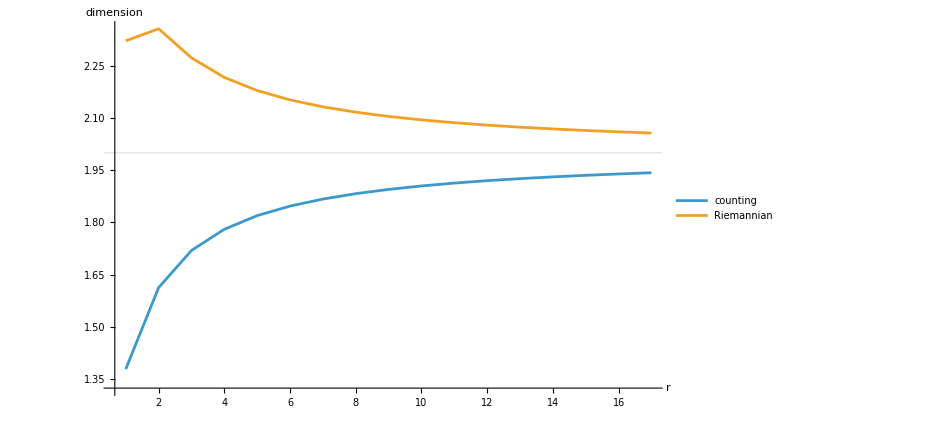

```mathematica
With[
  { graph = GridGraph[ { 41, 41 } ] },
  { centre = First @ GraphCenter[ graph ] },
  { regions = Table[ InfraBall[ centre, r ], { r, 1, 18 } ] },
  ListLinePlot[
    Map[ measure |-> LogDifferenceQuotients[ InfraMeasurement[ graph, regions, measure ] ],
      { "CountingMeasure", "RiemannianMeasure" } ],
    PlotLegends -> { "counting", "Riemannian" }, AxesLabel -> { "r", "dimension" },
    GridLines -> { None, { 2 } }, PlotRange -> All, ImageSize -> 700 ] ]
```

A radius-zero ball contains only its centre and does not resolve a dimension. A useful scale window requires many hops inside the region and enough room before the graph boundary. The lattice calculation proves a volume limit; the sampled example illustrates it under a different construction. Neither establishes a continuum limit for an arbitrary graph family.

## Related readings

Dimension compares growth measured in vertices and covering balls.

InfraShell, InfraTube, InfraQuadric, InfraCone and InfraSphere define other regions measured by InfraMeasurement.

Related Guides

RiemannianInfrageometrypaclet:WolframInstitute/InfraGeometry/guide/RiemannianInfrageometry ▪ EuclideanInfrageometrypaclet:WolframInstitute/InfraGeometry/guide/EuclideanInfrageometry

Related Tech Notes

## Metadata

### Categorization

Tutorial

WolframInstitute/InfraGeometry

WolframInstitute`InfraGeometry`

WolframInstitute/InfraGeometry/tutorial/VolumeMeasurementTutorial

### Keywords

volume

ball

tube

ellipsoid

counting measure

Riemannian measure

Rips graph

scaling limit

dimension

log-difference quotient